## Eigenvalue problems with NDSolve?

### Mathematica tutorial on b-splines

Plot it:

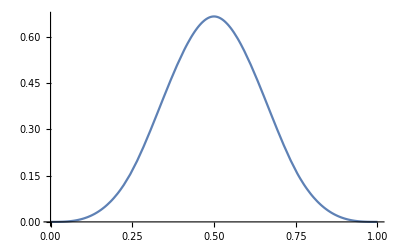

```mathematica
Plot[BSplineBasis[3,0,x],{x,0,1}]
```

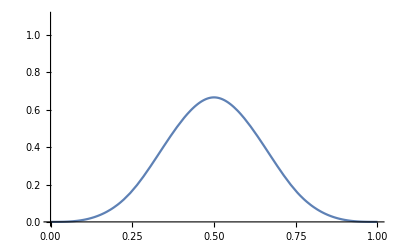

```mathematica
Plot[BSplineBasis[3,0,x],{x,0,1},PlotRange->{0,1.1}]
```

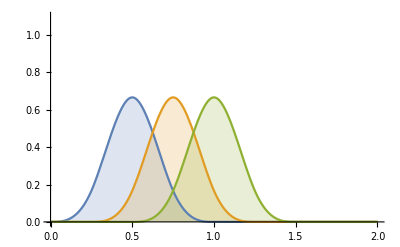

```mathematica
Plot[Evaluate[Table[BSplineBasis[3,i,x],{i,0,2}]],{x,0,2},PlotRange->{0,1.1},Filling->Axis,FillingStyle->Automatic]
```

Evaluate the second cubic B-spline basis with given knots:

```mathematica
knots={0,0,0,0,1/3,2/3,1,1,1,1};
```

```mathematica
BSplineBasis[{3,knots},2,0.5]
```

0.46875

```mathematica
knots[[2;;Length[knots]-1]]
```

{0,0,0,1/3,2/3,1,1,1}

Plot all the cubic basis functions with given knots:

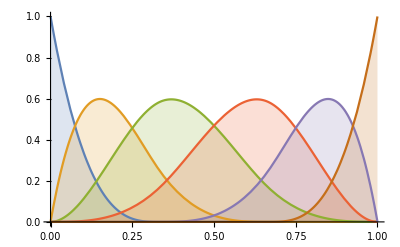

```mathematica
Plot[Evaluate[Table[BSplineBasis[{3,knots},i,x],{i,0,5}]],{x,0,1},Filling->Axis,FillingStyle->Automatic]
```

How do we deal with integrals of b-splines with arbitrary functions, for example when calculating matrix elements of the potential energy?  Say V_mn=∫ⅆx B_m(x)V(x)B_n(x).

```mathematica
V[x_,L_,V0_]:=V0/Cosh[x/L]^2
```

```mathematica
Vtable=Table[{x,V[x,1,-1]},{x,xmin,xmax,dx}]
```

{{0,-1},{10/9,-Sech[10/9]^2},{20/9,-Sech[20/9]^2},{10/3,-Sech[10/3]^2},{40/9,-Sech[40/9]^2},{50/9,-Sech[50/9]^2},{20/3,-Sech[20/3]^2},{70/9,-Sech[70/9]^2},{80/9,-Sech[80/9]^2},{10,-Sech[10]^2}}

### Generalize to arbitrary order:

```mathematica
m=10;xmin=0.0;xmax=10.0;dx=(xmax-xmin)/(m-1);
grid = Range[xmin,xmax,dx];
d = 3;
NumBasis=m+d-1;
knots=PadRight[PadLeft[grid,m+d],m+2d,xmax]
```

{0,0,0,0.,1.11111,2.22222,3.33333,4.44444,5.55556,6.66667,7.77778,8.88889,10.,10.,10.,10.}

```mathematica
Plot[Evaluate[Table[BSplineBasis[{d,knots},i,x],{i,0,NumBasis-1}]],{x,xmin,xmax},PlotRange->All,GridLines->{grid,{0,.25,.5,.75,1}}];
```

```mathematica
PiecewiseExpand[BSplineBasis[{d,knots},0,x]]
```

Piecewise[{{1.-2.7 x+2.43 x^2-0.729 x^3, 0.≤x≤1.11111}, {0, True}}]

```mathematica
PiecewiseExpand[MyBSpline[d,m,knots,1,x,1,0]]
```

Piecewise[{{3.-5.4 x+3.645 x^2-0.91125 x^3, x==1.11111}, {2.-2.7 x+1.215 x^2-0.18225 x^3, 1.11111<x≤2.22222}, {1.-1.215 x^2+0.54675 x^3, 0.≤x<1.11111}, {0, True}}]

```mathematica
xlast[ib_,jb_]:=Min[knots[[ib-1+d+2]],knots[[jb-1+d+2]]];
xfirst[ib_,jb_]:=Max[knots[[ib]],knots[[jb]]];
IRange[ib_,jb_]:=Module[{temp={xfirst[ib,jb],xlast[ib,jb]}},If[temp[[1]]<temp[[2]],temp,{0,0}]]
```

```mathematica
Table[IRange[ii,jj],{ii,1,NumBasis},{jj,1,NumBasis}]//MatrixForm
```

((0
1.11111) | (0
1.11111) | (0
1.11111) | (0.
1.11111) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(0
1.11111) | (0
2.22222) | (0
2.22222) | (0.
2.22222) | (1.11111
2.22222) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(0
1.11111) | (0
2.22222) | (0
3.33333) | (0.
3.33333) | (1.11111
3.33333) | (2.22222
3.33333) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(0.
1.11111) | (0.
2.22222) | (0.
3.33333) | (0.
4.44444) | (1.11111
4.44444) | (2.22222
4.44444) | (3.33333
4.44444) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(0
0) | (1.11111
2.22222) | (1.11111
3.33333) | (1.11111
4.44444) | (1.11111
5.55556) | (2.22222
5.55556) | (3.33333
5.55556) | (4.44444
5.55556) | (0
0) | (0
0) | (0
0) | (0
0)
(0
0) | (0
0) | (2.22222
3.33333) | (2.22222
4.44444) | (2.22222
5.55556) | (2.22222
6.66667) | (3.33333
6.66667) | (4.44444
6.66667) | (5.55556
6.66667) | (0
0) | (0
0) | (0
0)
(0
0) | (0
0) | (0
0) | (3.33333
4.44444) | (3.33333
5.55556) | (3.33333
6.66667) | (3.33333
7.77778) | (4.44444
7.77778) | (5.55556
7.77778) | (6.66667
7.77778) | (0
0) | (0
0)
(0
0) | (0
0) | (0
0) | (0
0) | (4.44444
5.55556) | (4.44444
6.66667) | (4.44444
7.77778) | (4.44444
8.88889) | (5.55556
8.88889) | (6.66667
8.88889) | (7.77778
8.88889) | (0
0)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (5.55556
6.66667) | (5.55556
7.77778) | (5.55556
8.88889) | (5.55556
10.) | (6.66667
10.) | (7.77778
10.) | (8.88889
10.)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (6.66667
7.77778) | (6.66667
8.88889) | (6.66667
10.) | (6.66667
10.) | (7.77778
10.) | (8.88889
10.)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (7.77778
8.88889) | (7.77778
10.) | (7.77778
10.) | (7.77778
10.) | (8.88889
10.)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (8.88889
10.) | (8.88889
10.) | (8.88889
10.) | (8.88889
10.))

```mathematica
it=1;jt=2;
VinterpPoints=N[Table[{x,V[x,1,-1]},{x,xmin,xmax,(xmax-xmin)/(3m-1)}]];
Vinterp[y_]:=InterpolatingPolynomial[VinterpPoints,y];
Plot[{Vinterp[y],V[y,1,-1]},{y,xmin,xmax},PlotRange->All];ClearSystemCache[];Timing[Integrate[BSplineBasis[{d,knots},it-1,x]BSplineBasis[{d,knots},jt-1,x]Vinterp[x],{x,0,10}]]
ClearSystemCache[];Timing[NIntegrate[BSplineBasis[{d,knots},it-1,x]BSplineBasis[{d,knots},jt-1,x]V[x,1,-1],{x,0,10}]]
ClearSystemCache[];Timing[Module[{ir=IRange[it,jt]},NIntegrate[BSplineBasis[{d,knots},it-1,x]BSplineBasis[{d,knots},jt-1,x]V[x,1,-1],{x,ir[[1]],ir[[2]]}]]]
Timing[NIntegrate[BSplineBasis[{d,knots},it-1,x]BSplineBasis[{d,knots},jt-1,x]V[x,1,-1],{x,IRange[it,jt][[1]],IRange[it,jt][[2]]}]]
```

{0.106789,-0.0869217}

{0.012748,-0.0868935}

{0.010983,-0.0868935}

{0.010934,-0.0868935}

### For the case of bound states with the wavefunction vanishing at the left and right boundary,

```mathematica
m=10;xmin=0;xmax=10.0;dx=(xmax-xmin)/(m-1);
grid = Range[xmin,xmax,dx];
grid = Table[xmin + ((i-1)/(m-1))^2(xmax-xmin),{i,1,m}]
```

{0.,0.123457,0.493827,1.11111,1.97531,3.08642,4.44444,6.04938,7.90123,10.}

```mathematica
d = 3;
NumBasis=m+d-3;
knots=PadRight[PadLeft[grid,m+d-1,xmin],m+2d-2,xmax]
```

{0,0,0.,0.123457,0.493827,1.11111,1.97531,3.08642,4.44444,6.04938,7.90123,10.,10.,10.}

```mathematica
Plot[Evaluate[Table[BSplineBasis[{d,knots},i,x],{i,2,3}]],{x,xmin,xmax},PlotRange->All,GridLines->{grid,{0,.25,.5,.75,1}}];
```

```mathematica
xlast[ib_,jb_]:=Min[knots[[ib+d+1]],knots[[jb+d+1]]];
xfirst[ib_,jb_]:=Max[knots[[ib]],knots[[jb]]];
IRange[ib_,jb_]:=Module[{temp={xfirst[ib,jb],xlast[ib,jb]}},If[temp[[1]]<temp[[2]],temp,{0,0}]]
```

### Set up some the overlap and hamiltonian matrices for the harmonic oscillator

```mathematica
VHO[x_]:=1/2 x^2
```

The overlap matrix S, potential V, and kinetic energy T,  To do this right, I’ll eventually need to only calculate the nonzero matrix elements.

```mathematica
IRange[1,1]
```

{0,0.493827}

```mathematica
ir=Table[IRange[ib,jb],{ib,1,NumBasis},{jb,1,NumBasis}];
```

```mathematica
Timing[
S=Table[
If[ir[[ib,jb]][[1]]<ir[[ib,jb]][[2]],
NIntegrate[BSplineBasis[{d,knots},ib-1,x]BSplineBasis[{d,knots},jb-1,x],{x,ir[[ib,jb]][[1]],ir[[ib,jb]][[2]]}],0],{ib,1,NumBasis},{jb,1,NumBasis}];
V=Table[
If[ir[[ib,jb]][[1]]<ir[[ib,jb]][[2]],
NIntegrate[BSplineBasis[{d,knots},ib-1,x]VHO[x]BSplineBasis[{d,knots},jb-1,x],{x,ir[[ib,jb]][[1]],ir[[ib,jb]][[2]]}],0],{ib,1,NumBasis},{jb,1,NumBasis}];
T=
Table[
If[ir[[ib,jb]][[1]]<ir[[ib,jb]][[2]],
NIntegrate[1/2 D[BSplineBasis[{d,knots},ib-1,x],x]D[BSplineBasis[{d,knots},jb-1,x],x],{x,ir[[ib,jb]][[1]],ir[[ib,jb]][[2]]}],0],{ib,1,NumBasis},{jb,1,NumBasis}];
H=T+V;
Eigensystem[{H,S}][[1]]]
```

{3.31761,{158.437,42.4745,30.7652,20.3221,19.689,11.9744,7.57646,5.81585,3.52461,1.50088}}

```mathematica
Timing[S=Table[NIntegrate[BSplineBasis[{d,knots},ib-1,x]BSplineBasis[{d,knots},jb-1,x],{x,IRange[ib,jb][[1]],IRange[ib,jb][[2]]}],{ib,1,NumBasis},{jb,1,NumBasis}];
V=Table[NIntegrate[BSplineBasis[{d,knots},ib-1,x]VHO[x]BSplineBasis[{d,knots},jb-1,x],{x,IRange[ib,jb][[1]],IRange[ib,jb][[2]]}],{ib,1,NumBasis},{jb,1,NumBasis}];
T=Table[NIntegrate[-1/2 BSplineBasis[{d,knots},ib-1,x]D[D[BSplineBasis[{d,knots},jb-1,x],x],x],{x,IRange[ib,jb][[1]],IRange[ib,jb][[2]]}],{ib,1,NumBasis},{jb,1,NumBasis}];
H=T+V;
Esys=Eigensystem[{H,S}];Esys[[1]]]
```

{172.689,{226.29,226.29,151.133,151.133,139.857,139.857,131.951,131.95,126.015,125.981,121.953,121.319,118.96,117.038,114.789,112.484,110.129,107.756,105.385,103.03,100.701,98.405,96.1481,93.9335,91.7633,89.6389,87.5607,85.5289,83.5431,81.6027,79.7068,77.8545,76.0449,74.277,72.5499,70.8625,69.2141,67.6038,66.0309,64.4948,62.9949,61.5309,60.1023,58.709,57.3508,56.0277,54.7396,53.4866,52.2685,51.0848,49.9346,48.8162,47.7266,46.6619,45.6173,44.5878,43.5686,42.556,41.5473,40.5409,39.5358,38.5315,37.5277,36.5243,35.5213,34.5186,33.5162,32.514,31.5121,30.5104,29.5089,28.5076,27.5064,26.5054,25.5045,24.5038,23.5031,22.5025,21.5021,20.5017,19.5013,18.501,17.5008,16.5006,15.5005,14.5004,13.5003,12.5002,11.5001,10.5001,9.50006,8.50004,7.50002,6.50001,5.50001,4.5,3.5,2.5,1.5,0.5}}

```mathematica
Timing[S=Table[NIntegrate[BSplineBasis[{d,knots},ib-1,x]BSplineBasis[{d,knots},jb-1,x],{x,xmin,xmax}],{ib,1,NumBasis},{jb,1,NumBasis}];
V=Table[NIntegrate[BSplineBasis[{d,knots},ib-1,x]VHO[x]BSplineBasis[{d,knots},jb-1,x],{x,xmin,xmax}],{ib,1,NumBasis},{jb,1,NumBasis}];
T=Table[NIntegrate[-1/2 BSplineBasis[{d,knots},ib-1,x]D[D[BSplineBasis[{d,knots},jb-1,x],x],x],{x,xmin,xmax}],{ib,1,NumBasis},{jb,1,NumBasis}];
H=T+V;
Eigensystem[{H,S}][[1]]]
```

{271.13,{226.29,226.29,151.133,151.133,139.857,139.857,131.951,131.95,126.015,125.981,121.953,121.319,118.96,117.038,114.789,112.484,110.129,107.756,105.385,103.03,100.701,98.405,96.1481,93.9335,91.7633,89.6389,87.5607,85.5289,83.5431,81.6027,79.7068,77.8545,76.0449,74.277,72.5499,70.8625,69.2141,67.6038,66.0309,64.4948,62.9949,61.5309,60.1023,58.709,57.3508,56.0277,54.7396,53.4866,52.2685,51.0848,49.9346,48.8162,47.7266,46.6619,45.6173,44.5878,43.5686,42.556,41.5473,40.5409,39.5358,38.5315,37.5277,36.5243,35.5213,34.5186,33.5162,32.514,31.5121,30.5104,29.5089,28.5076,27.5064,26.5054,25.5045,24.5038,23.5031,22.5025,21.5021,20.5017,19.5013,18.501,17.5008,16.5006,15.5005,14.5004,13.5003,12.5002,11.5001,10.5001,9.50006,8.50004,7.50002,6.50001,5.50001,4.5,3.5,2.5,1.5,0.5}}

### Some more random plots of bsplines

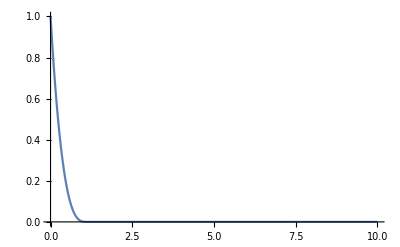
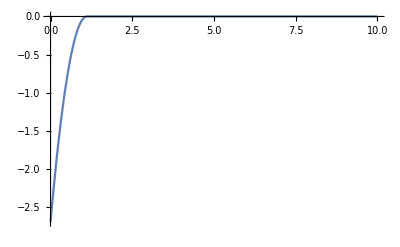
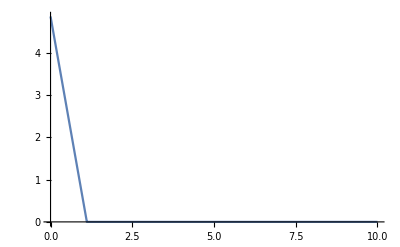
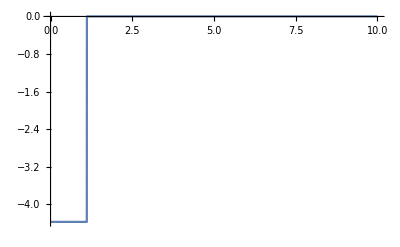

```mathematica
Table[Plot[Evaluate[D[BSplineBasis[{d,knots},0,x],{x,i}]],{x,xmin,xmax},PlotRange->All],{i,0,d}]
```

```mathematica
Table[Plot[Evaluate[D[BSplineBasis[{d,knots},0,x],{x,i}]],{x,xmin,xmax},PlotRange->All],{i,0,d}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

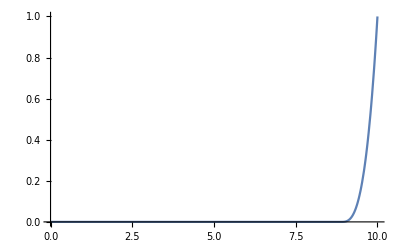
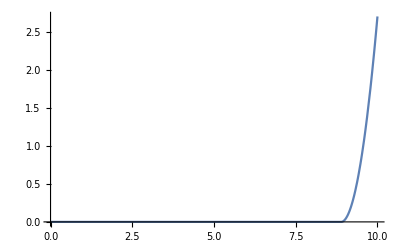
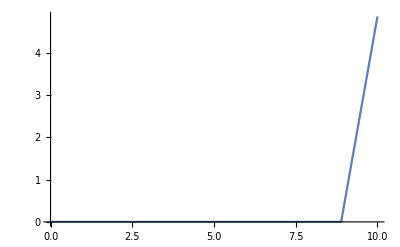
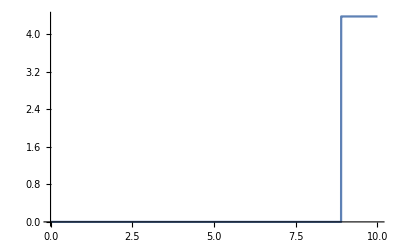

```mathematica
Table[Plot[Evaluate[D[BSplineBasis[{d,knots},m+d-2,x],{x,i}]],{x,xmin,xmax},PlotRange->All],{i,0,d}]
```

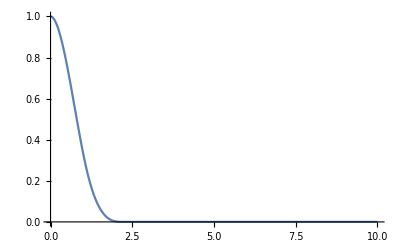
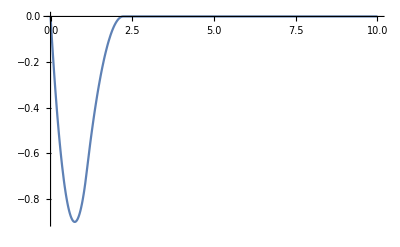
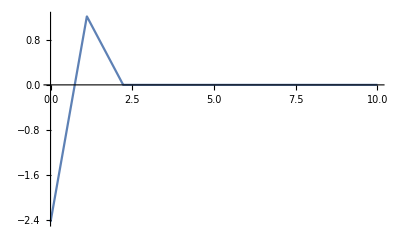
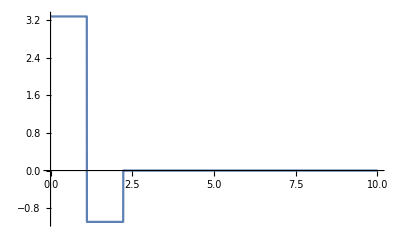

```mathematica
Table[Plot[Evaluate[D[BSplineBasis[{d,knots},0,x]+BSplineBasis[{d,knots},1,x],{x,i}]],{x,xmin,xmax},PlotRange->All],{i,0,d}]
```

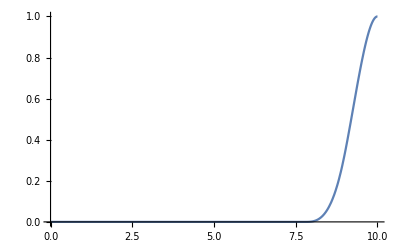

```mathematica
Plot[BSplineBasis[{d,knots},m+d-3,x]+BSplineBasis[{d,knots},m+d-2,x],{x,xmin,xmax},PlotRange->All]
```

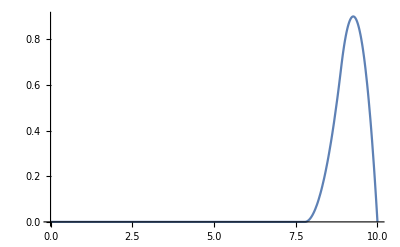
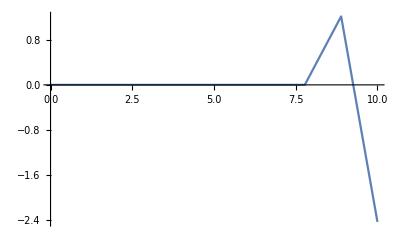
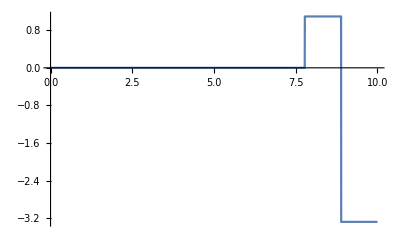
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[Evaluate[D[BSplineBasis[{d,knots},m+d-3,x]+BSplineBasis[{d,knots},m+d-2,x],{x,i}]],{x,xmin,xmax},PlotRange->All],{i,0,3}]
```

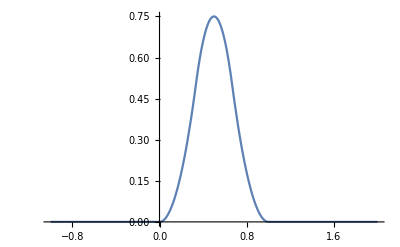

```mathematica
Plot[BSplineBasis[2,x],{x,-1,2},PlotRange->All]
```